```mathematica
PinwheelArea[alpha_,beta_,a_]:= Module[{gamma,b,c,ap,bp,cp,alphap,betap,gammap,ra,rb,rc,tha,thb,thc,e,la,lb,lc,print},
print=False;
e = Sin[Pi/5];
gamma = Pi/5 - (alpha+beta);
alphap = 2Pi/5 - alpha;
betap = 2Pi/5-beta;
gammap = 2Pi/5 - gamma;
b = a * Sin[betap]/Sin[alphap];
c = a * Sin[gammap]/Sin[alphap];
ap = e - a;
bp = e - b;
cp = e - c;
tha = ArcTan[ap/rho];
thb = ArcTan[bp/rho];
thc = ArcTan[cp/rho];
ra = ap/Sin[tha];
rb = bp/Sin[thb];
rc = cp/Sin[thc];
la =Sqrt[1+rb^2 - 2 rb Cos[Pi/2-thb+alpha+3Pi/10]];
lb = Sqrt[1+rc^2 - 2rc Cos[Pi/2-thc + beta+3Pi/10]];
lc = Sqrt[1+ra^2 - 2 ra Cos[Pi/2-tha+gamma+3Pi/10]];
If[print,Print[{e,{a,b,c},{ap,bp,cp},{alpha,beta,gamma},{alphap,betap,gammap},{tha,thb,thc},{ra,rb,rc},{la,lb,lc}}//N]];
area[la,lb,lc]
];
```

```mathematica
Clear[interp];
interp[p1_,p2_,x_]:= Module[{x1,y1,x2,y2},
{x1,y1}=p1;
{x2,y2}=p2;
(y2-y1)/(x2-x1) (x - x1) + y1];
```

```mathematica
interp[{1.878,1.237},{2.1,1.291},2]
```

1.26668

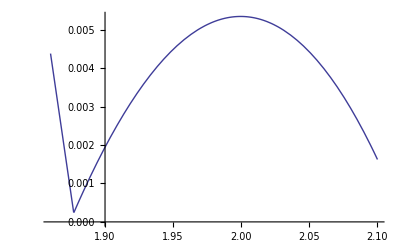

```mathematica
Plot[Max[1.237,area[2rho,2rho,x]]-interp[{1.878,1.237},{2.1,1.291},x],{x,1.86,2.1}]
```

```mathematica
0.
```

```mathematica
pinwheelarea[0.209439510239319421,0.209439510239319532,0.181048620887643535]
```

1.2848445560030345

```mathematica
D[area[u,u,x],{x,2}]//Simplify//Factor
```

-(u^2 √((x^2 (4 u^2-x^2))/u^4) (6 u^2-x^2))/(2 (2 u-x)^2 (2 u+x)^2)

```mathematica
area[u,u,x]//Factor
```

1/4 u^2 √((x^2 (4 u^2-x^2))/u^4)

```mathematica
Minimize[{1/s1 + 1.0/t1,ArcTan[s1]+ArcTan[t1]≤ 2.2,1≤ s1,1≤ t1},{s1,t1}]
```

{1.01794,{s1→1.96476,t1→1.96476}}

```mathematica
(* save: calculation of local twist-max on interval *)
Clear[t];
epsI=N[5/1000,50];
piN = N[Pi,50];
epsII = Interval[{0,epsI}];
epsI2 = Interval[{-epsI,epsI}];
alphat=piN/5 + epsII+ t;
betat = 2piN/5+epsI2; (* fix betat *)
gammat = piN - (alphat+betat); 
xgammat = ee+epsI2;
alphap = epsII; (* fix alphap *)
gammap = 2piN/5 - alphat; (* relate two sides *)
betap = (piN/5 - (alphap+gammap)); (* drag betap*)
xgammap = ee +epsI2;
D[(tjarea[alphat,betat,xgammat]+
pinwheelarea[alphap,betap,xgammap]),t]/.{t->0}
```

```mathematica
(* save: calculation of local twist-max on interval *)
Clear[t];
epsI=N[5/1000,50];
piN = N[Pi,50];
epsII = Interval[{0,epsI}];
epsI2 = Interval[{-epsI,epsI}];
alphat=piN/5 + epsII+ t;
gammat = 2piN/5+epsI2; (* fix gammat *)
betat = piN - (alphat+gammat); 
xgammat = ee+epsI2;
betap = epsII; (* fix betap *)
gammap = 2piN/5 - alphat; (* relate two sides *)
alphap = (piN/5 - (betap+gammap)); (* drag alphap*)
xgammap = ee +epsI2;
D[(tjarea[alphat,betat,xgammat]+
pinwheelarea[alphap,betap,xgammap]),t]/.{t->0}
```

```mathematica
(* calculation of slider double lattice second derivative.  By symmetry there is a unique zero at t=0, so this gives local optimality. *)
epsI=N[1/50,50];
epsI2 = Interval[{-epsI,epsI}];
D[pinwheelarea[0,0,ee+epsI2+t]+pinwheelarea[0,0,ee+epsI2-t],{t,2}]/.t->0
```

Interval[{0.2870748239214178815701788443868756481071914133972,2.0465952255300542245831681144974245340491118188607}]

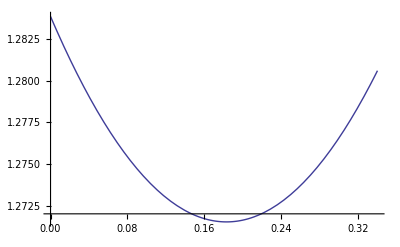

```mathematica
Plot[pinwheelarea[0.1,0.1,t],{t,0,0.34}]
```

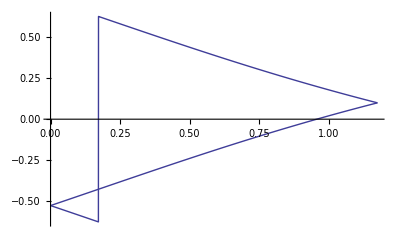

```mathematica
Plot[thetax[x,0.2],{x,0,2ee}]
```

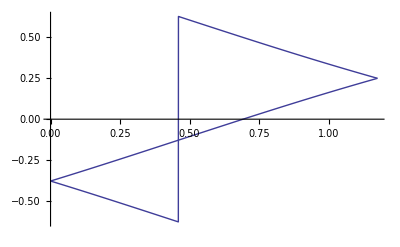

```mathematica
Plot[thetax[xalpha,0.5],{xalpha,0,2ee}]
```

```mathematica
?lawsines
```

Global`lawsines

lawsines[a_,alpha_,beta_,gamma_]:=(a {Sin[beta],Sin[gamma]})/Sin[alpha]

```mathematica
2ee//N
```

1.17557

```mathematica
pointer2[beta_,alpha_]:= Module[{phi,gamma,va,wa,xa,bb},
phi = 3Pi/10;
gamma = Pi - alpha-beta;
{va,wa}=lawsines[2ee,beta,gamma,alpha];
xa = loc[1,va,phi+alpha];
bb = arc[xa,va,1];
xa*{Cos[bb],Sin[bb]}
];
pointrecept[t_,alpha_]:=Module[{gamma,phi,a,r},
gamma = 2Pi/5-alpha;
phi = 3Pi/10;
a = t/Sin[gamma];
r = {-a * Cos[gamma],-t};
r + {Cos[gamma+phi],Sin[gamma+phi]}
];
```

```mathematica
pointer2[0.1,0.1]
```

{1.83531,0.863656}

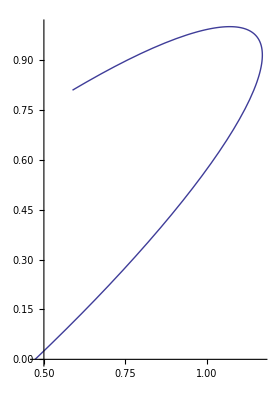

```mathematica
ParametricPlot[pointer2[1.4,t],{t,0,7Pi/10}]
```

```mathematica
ffj[t_]:=ParametricPlot[pointrecept[t,alpha],{alpha,0,2Pi/5 - ArcSin[t/(2ee)]}]
```

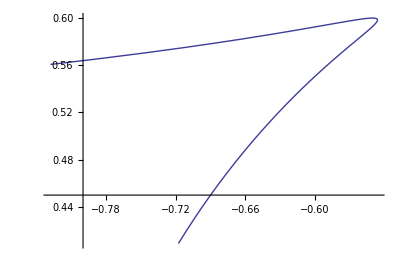

```mathematica
ffj[0.4]
```

```mathematica
2Pi/5.0
```

1.25664

```mathematica
2ee//N
```

1.17557

```mathematica
Solve[area[1.78,1.78,x]==areadl,x]
```

{{x→-3.16434},{x→-1.63113},{x→1.63113},{x→3.16434}}

```mathematica
(x/.Solve[eta[x,x,2]==Sqrt[3],x])
```

{-3.301360247771569,-1.049295246550581,1.049295246550581,3.301360247771569}

```mathematica
eta[xz,xz,2]^2
```

3.

```mathematica
eps = 10^-8; xx = Sqrt[8]-eps;
volxx = Sqrt[Delta[xx,2,2,xx,2,2]]/12//N;
solxx = 4 Solid[xx,2,2,xx,2,2];
solxx/(3 volxx)
```

0.585786

```mathematica
4 Solid[xx,2,2,
```

0.000224239

```mathematica
rhoxz/volxz//N
```

0.784688

```mathematica
rhoxz = 1/3(Solid[xz,xz,2,2,2,2]+Solid[xz,2,2,2,xz,2]2+Solid[2,2,2,xz,xz,2])
```

1/3 (-2 π+2 ArcCos[(-16-16 (3+√6)+4 (12+2 (3+√6)))/(4 √(3 (32 (3+√6)-4 (3+√6)^2)))]+2 ArcCos[(-16 (3+√6)-4 (3+√6)^2+2 (3+√6) (12+2 (3+√6)))/(√((-16+32 (3+√6)) (32 (3+√6)-4 (3+√6)^2)))]+2 (-π+ArcCos[(-16-16 (3+√6)+4 (12+2 (3+√6)))/(4 √(3 (32 (3+√6)-4 (3+√6)^2)))]+ArcCos[(-16 (3+√6)-4 (3+√6)^2+2 (3+√6) (12+2 (3+√6)))/(√((-16+32 (3+√6)) (32 (3+√6)-4 (3+√6)^2)))]+ArcCos[(-48+4 (8+4 (3+√6)))/(4 √(3 (-16+32 (3+√6))))])+2 ArcCos[(-64+16 (3+√6)-4 (3+√6)^2+4 (8+4 (3+√6)))/(32 (3+√6)-4 (3+√6)^2)])

```mathematica
volxz=Sqrt[Delta[xz,xz,2,2,2,2]//Expand]/12
```

1/12 √(80+32 √6)

```mathematica
xz = Sqrt[2(3+Sqrt[6])];
xz//N
```

3.30136

```mathematica
Solve[Rad[x,x,2,2,2,2]==2,x]
```

{{x→-√(2 (3-√6))},{x→√(2 (3-√6))},{x→-√(2 (3+√6))},{x→√(2 (3+√6))}}